```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\DK\OneDrive - Duke University\_Doc\repositories\fishbonett\examples

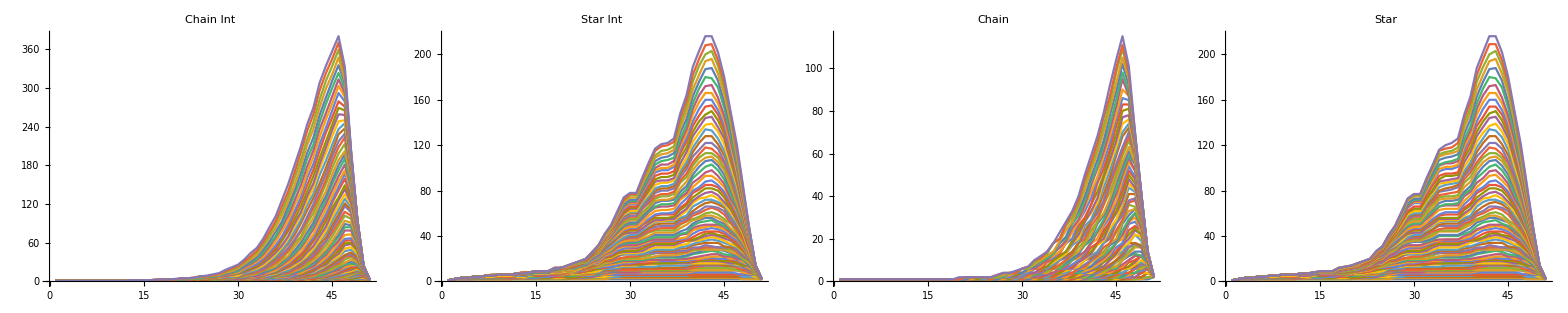

```mathematica
data1=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap.dat","Real32"]];data2=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_star1.dat","Real32"]];data3=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_chain.dat","Real32"]];data4=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_star_int.dat","Real32"]];
llpset={ColorFunction-> "SouthwestColors"};
Grid[{
{ListLinePlot[data1,PlotRange->All,PlotLabel->"Chain Int"],
ListLinePlot[data4,PlotRange->All,PlotLabel->"Star Int"],
ListLinePlot[data3,PlotRange->All,PlotLabel->"Chain"],
ListLinePlot[data2,PlotRange->All,PlotLabel->"Star"]
}}
]
```

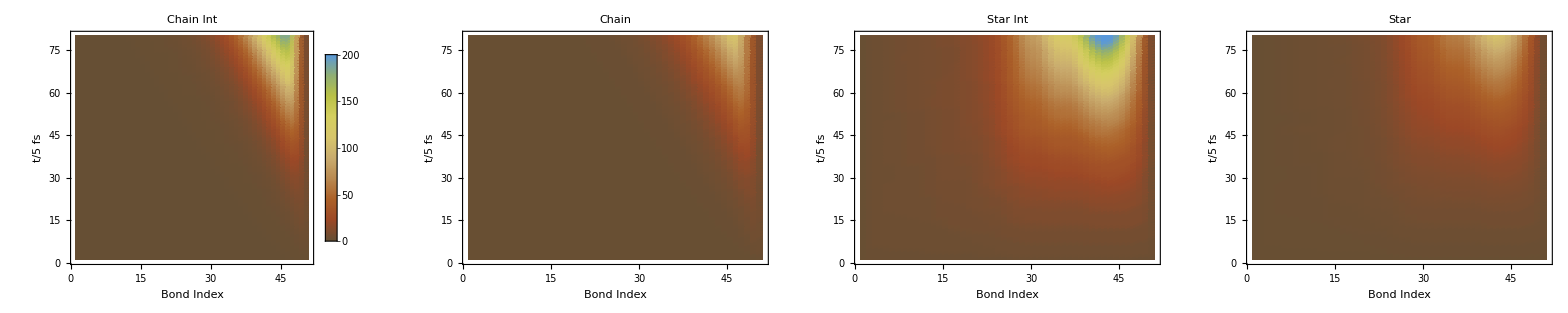

```mathematica
ldpset={PlotRange->Full,ColorFunctionScaling->False,ColorFunction->"SouthwestColors",LabelStyle->{FontFamily->"DejaVu Sans",13},FrameLabel->{"Bond  Index","t/5 fs"}};Legended[#,BarLegend[{"SouthwestColors",{0,200}},LegendMarkerSize->120]]&[Grid[{
{ListDensityPlot[data1/400,ldpset,PlotLabel->"Chain  Int"],
ListDensityPlot[data3/200,ldpset,PlotLabel->"Chain"],
ListDensityPlot[data4/200,ldpset,PlotLabel->"Star  Int"],
ListDensityPlot[data2/400,ldpset,PlotLabel->"Star"]
}},ItemSize->15,Spacings->{0, 0}
]
]
```

```mathematica
(*spectral density*)gam=100/1.8;drude=2* (100/Pi)*gam(x/(x^2+gam^2));

(*weight function is the square of ψ*)
w=drude;

(*norm of the weight function*)
normw=1;

(*normalized weight function*)
wnormed=w/normw;

(*orthogonalizes the monomials 1,x,x^2,x^3,...,x^n assuming an inner-product convolution with normalized weight fn*)
symbasis[n_?IntegerQ]:=Orthogonalize[x^#&/@Range[0,n],Integrate[wnormed*#1*#2,{x,0,350}]&]
```

```mathematica
k=Simplify[symbasis[7]]
```

{0.0123526,0.000133955 (-146.508+x),0.0297571-0.000515589 x+1.52766×10^-6 x^2,-0.0415107+0.00126689 x-9.04628×10^-6 x^2+1.7492×10^-8 x^3,0.0546085-0.00253474 x+0.000031369 x^2-1.39162×10^-7 x^3+2.00339×10^-10 x^4,-0.0689017+0.00448317 x-0.0000833972 x^2+6.23031×10^-7 x^3-1.99844×10^-9 x^4+2.29389×10^-12 x^5,0.0842886-0.00729112 x+0.000188055 x^2-2.07128×10^-6 x^3+1.09593×10^-8 x^4-2.74987×10^-11 x^5+2.6257×10^-14 x^6,-0.100692+0.0111512 x-0.000378398 x^2+5.69624×10^-6 x^3-4.37533×10^-8 x^4+1.78443×10^-10 x^5-3.67506×10^-13 x^6+3.00472×10^-16 x^7}

```mathematica
Plot[Table[Re[NIntegrate[k[[i]]* Cos[x t],{x,0,350}]],{i,1,7}],{t,0,0.2},PlotRange->Full,PlotLegends->Automatic]
```

$Aborted

```mathematica
NIntegrate[{x^2,x^3}* Cos[x ],{x,0,350}]
```

{-117666.,-4.12165×10^7}

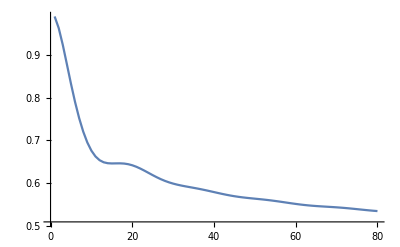

```mathematica
ListLinePlot[{0.9901906945836054,0.9628938019269295,0.9234646027388752,0.8781993788036828,0.8323968834258588,0.7896157747908176,0.7518756553934937,0.7201508774303556,0.6947514705166388,0.6755225761580708,0.6619427997395939,0.653200812870264,0.6482867737517772,0.6461016135270421,0.6455691281767647,0.645732823762519,0.64582403435032,0.6452959291936698,0.6438267867317322,0.6413007999007259,0.6377726378999318,0.6334226655485798,0.6285080714669937,0.6233162397264216,0.618125973631889,0.6131762246409147,0.6086449347808371,0.604639591401108,0.6011967233925698,0.5982899865338077,0.595844008041069,0.5937513878824361,0.5918913569587714,0.5901459678942693,0.5884134396399974,0.586618980128742,0.5847196963377488,0.5827051246614062,0.5805944685361042,0.5784290637006424,0.5762644983392144,0.5741619631078729,0.5721776282965593,0.5703555307796646,0.5687225720563513,0.5672845297406641,0.5660272632288105,0.5649196552387372,0.5639168969688195,0.5629676930911731,0.562021432079818,0.5610332072516461,0.5599688886795973,0.5588091547076435,0.557551835071381,0.5562108754788538,0.5548128833340936,0.5533941019374766,0.5519957757041799,0.5506578706200804,0.5494150044559619,0.5482925772651916,0.5473028826786974,0.5464446417919532,0.5457033906892272,0.545052861479663,0.5444595310170766,0.5438868939660565,0.5432986776987389,0.5426637770991144,0.5419600174470692,0.5411760016552501,0.5403124489955262,0.5393817324575447,0.5384059047962722,0.5374137166253715,0.5364367259891857,0.5355057252504661,0.5346468985388022,0.5338784163843046},PlotRange->Full]
```